```mathematica
Lab 5 : Detector Efficiency and Multidimensional Sources
J.R. Powers - Luhn
16 February 2017
Thursday
Lab Partner: Eric Francis
```

Pre-Laboratory Questions

1. What are the two main components of detection efficiency?

The two main components are geometric and intrinsic efficiency. Intrinsic efficiency is broken down into three sub-components: the density and size of detector material, the type and energy of the radiation, and the electronics in the detector system (Tsoulfanidis 259). Geometric efficiency has to do with the solid angle presented by the detector.

2. Using the NIST database, determine the linear and mass attenuation coefficient of air for the primary gamma from Cs-137 and Co-60.

Primary gamma for Cs-137 is 661.657 keV, primary gammas for Co-60 (co-emitted) are 1173.237 keV and 1332.501 keV.

```mathematica
{{Nuclide, Energy (keV), Linear Attenuation Coefficient
(cm^-1), Mass Attenuation Coefficient
(cm^2/g)}, {Cs-137, 661.657, 9.49690121e-05, 0.0775257}, {Co-60, 1173.237, 7.21896407e-05, 0.05893032}, {□, 1332.501, 6.75959649e-05, 0.05518038}}
```

{{Nuclide,Energy keV,(Attenuation Coefficient Linear)/cm,(Attenuation cm^2 Coefficient Mass)/g},{-137+Cs,661.657,-5+9.4969 e,0.0775257},{-60+Co,1173.24,-5+7.21896 e,0.0589303},{□,1332.5,-5+6.7596 e,0.0551804}}

3. Using the NNDC database, find the emission probability of energetic photons (x-rays and gamma-rays) above 30 keV for Cs-137 and Co-60.

```mathematica
Cs - 137
```

```mathematica
{{Energy (keV), Intensity (%)}, {31.817, 1.99}, {32.194, 3.64}, {36.304, 0.348}, {36.378, 0.672}, {37.255, 0.213}, {283.5, 5.8e-4}, {661.657, 85.10}}
```

{{Energy keV,{{86.36 Intensity,5.53333 Intensity},Intensity ErrorBar[5.,5.]}},{31.817,1.99},{32.194,3.64},{36.304,0.348},{36.378,0.672},{37.255,0.213},{283.5,-4+5.8 e},{661.657,85.1}}

```mathematica
Co-60
```

```mathematica
{{Energy (keV), Intensity (%)}, {347.14, 0.0075}, {826.10, 0.0076}, {1173.228, 99.85}, {1332.492, 99.9826}, {2158.57, 0.00120}, {2505.692, 2.0e-6}}
```

4. In the rule of thumb described below, justify this assumption based upon angle and curvature arguments and estimate the uncertainty in the assumed projected detector area for a point source.

At this distance (~ 3 √A), the error in the solid angle is approximately 1%. Any greater distance will reduce this error even further. Therefore we can ignore the specific geometry of the area source and treat the source as a point.

In-Lab

```mathematica
BackgroundFileName="background.tsv";
BackgroundCounts=Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,3]]]
BackgroundTime=Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
BackgroundCountRate=BackgroundCounts/Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
```

171

300.

0.57

```mathematica
BackgroundCountRateError=√BackgroundCounts/Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
```

0.043589

The Background count rate is 0.57±0.04 cps

```mathematica
Import[NotebookDirectory[]<>BackgroundFileName]
```

{{Description,},{Number of Runs,5},{Preset Time,60},{Preset Counts,0},{Pause Time,0},{Alarm Level,0},{High Voltage,900},{},{Run,High,,Elapsed},{Number,Voltage,Counts,Time,Date/Time,Notes},{},{1,900,35,60.,02/16/2017 06:06:28 PM,},{2,900,25,60.,02/16/2017 06:07:29 PM,},{3,900,47,60.,02/16/2017 06:08:30 PM,},{4,900,29,60.,02/16/2017 06:09:31 PM,},{5,900,35,60.,02/16/2017 06:10:32 PM,}}

Point Source

```mathematica
PartACsDetectorHeight={1+1/16, 3+1/16, 6+1/16, 9+1/16, 12+1/16} * 2.54 (* centimeters *);
```

```mathematica
PartACsRawCounts = {17612, 4548, 1357, 746, 501};
PartACsCountTimes = {190.8, 200, 200, 200, 200};
```

```mathematica
PartACoDetectorHeight={12+1/16, 9+1/8,6+1/16, 3+1/16, 1+1/16}*2.54//N;
PartACoRawCounts={426, 661, 1302, 3694, 16014};
PartACoCountTimes={200, 200, 200, 200, 200};
```

## Post-Lab

## Utility Functions

```mathematica
Needs["ErrorBarPlots`"]
(* Corrects the count rate for deadtime *)
tau=262*10^-6; (* deadtime in seconds *)
DTC[r_]:=r/(1+r*tau);
DTCError[v_,e_]=√((Derivative[1][DTC][v])^2*e^2)//N;
DoPlot[xlist_,ylist_,xerror_,yerror_]:=Table[{xlist[[i]],ylist[[i]]},ErrorBar[xerror[[i]],yerror[[i]]],{i,Length[xlist]}]
Radius=((1+5/16.)/2)*2.54 (* Radius of detector in cm *)
```

1.66688

```mathematica
Deadtime=262*10^-6;
```

```mathematica
muCsAir=0.0000949;
muCoAir=0.0000723;
```

Point Source

1. Determine the background count rate.

Performed in the lab section above. The background count rate is 0.57±0.04 cps.

2. Make a table for each isotope (i.e., Cs-137 and Co-60) that lists the source-detector distance, gross count rate, background corrected, background and dead time corrected count rate, and uncertainty in the background and dead time corrected count rate. Each data set identified should be a column in the dataset.

```mathematica
PartACsDetectorHeight (* from in-lab above *)
PartACsRawCounts(* from in-lab above *)
PartACsCountTimes (* from in-lab above *)
PartACsGrossCountRates = PartACsRawCounts / PartACsCountTimes//N
PartACsBGCorrectedCountRate = PartACsGrossCountRates-BackgroundCountRate
PartACsBGDTCorrectedCountRate=Table[DTC[PartACsBGCorrectedCountRate[[i]]],{i,Length[PartACsBGCorrectedCountRate]}]
PartACsBGDTCorrectedRateError=Table[DTCError[PartACsBGCorrectedCountRate[[i]],√PartACsBGCorrectedCountRate[[i]]], {i,Length[PartACsBGCorrectedCountRate]}]
```

{2.69875,7.77875,15.3988,23.0188,30.6388}

{17612,4548,1357,746,501}

{190.8,200,200,200,200}

{92.3061,22.74,6.785,3.73,2.505}

{91.7361,22.17,6.215,3.16,1.935}

{89.583,22.042,6.2049,3.15739,1.93402}

{9.13357,4.65428,2.48489,1.7747,1.38963}

Cs-137 Table

```mathematica
TableForm[Map[{PartACsDetectorHeight[[#]], PartACsGrossCountRates[[#]], PartACsBGCorrectedCountRate[[#]], PartACsBGDTCorrectedCountRate[[#]], PartACsBGDTCorrectedRateError[[#]]}&,{1,2,3,4,5}],TableHeadings->{None,{"Distance (cm)", "Count Rate (cps)", "BKG Corrected (cps)", "BKG-τ Corrected (cps)", "Error"}}]
```

Distance (cm) | Count Rate (cps) | BKG Corrected (cps) | BKG-τ Corrected (cps) | Error
2.69875 | 92.3061 | 91.7361 | 89.583 | 9.13357
7.77875 | 22.74 | 22.17 | 22.042 | 4.65428
15.3988 | 6.785 | 6.215 | 6.2049 | 2.48489
23.0188 | 3.73 | 3.16 | 3.15739 | 1.7747
30.6388 | 2.505 | 1.935 | 1.93402 | 1.38963

```mathematica
PartACoDetectorHeight (* from in-lab above *);
PartACoRawCounts(* from in-lab above *);
PartACoCountTimes (* from in-lab above *);
PartACoGrossCountRates = PartACoRawCounts / PartACoCountTimes//N
PartACoBGCorrectedCountRate = PartACoGrossCountRates-BackgroundCountRate
PartACoBGDTCorrectedCountRate=Table[DTC[PartACoBGCorrectedCountRate[[i]]],{i,Length[PartACoBGCorrectedCountRate]}]
PartACoBGTDCorrectedRateError=Table[DTCError[PartACoBGCorrectedCountRate[[i]],√PartACoBGCorrectedCountRate[[i]]],{i,Length[PartACoBGCorrectedCountRate]}]
```

{2.13,3.305,6.51,18.47,80.07}

{1.56,2.735,5.94,17.9,79.5}

{1.55936,2.73304,5.93077,17.8164,77.8779}

{1.24798,1.65142,2.42964,4.19143,8.55613}

Co-60 Table

```mathematica
TableForm[Map[{PartACoDetectorHeight[[#]]*2.54, PartACoGrossCountRates[[#]], PartACoBGCorrectedCountRate[[#]], PartACoBGDTCorrectedCountRate[[#]], PartACoBGTDCorrectedRateError[[#]]}&,{1,2,3,4,5}],TableHeadings->{None,{"Distance (cm)", "Count Rate (cps)", "BKG Corrected (cps)", "BKG-τ Corrected (cps)", "Error"}}]
```

Distance (cm) | Count Rate (cps) | BKG Corrected (cps) | BKG-τ Corrected (cps) | Error
77.8224 | 2.13 | 1.56 | 1.55936 | 1.24798
58.8709 | 3.305 | 2.735 | 2.73304 | 1.65142
39.1128 | 6.51 | 5.94 | 5.93077 | 2.42964
19.758 | 18.47 | 17.9 | 17.8164 | 4.19143
6.85483 | 80.07 | 79.5 | 77.8779 | 8.55613

3. For each source, determine the source energetic photon emission activity of each source with uncertainty. Assume that the source strength printed on each label is accurate to ±5%. Include source decay (see born date).

Cs-137 has a half life of 30.08yr. For each decay, there is a 91.963% chance of a photon emission with high enough energy to reach and trigger the detector. The source was born with an activity of 10μCi in April, 2011, meaning that it is 6*12-2=70 months old.

```mathematica
Activity[A0_,halflife_,time_,bf_]:=bf*A0*10^-6*3.7*10^10*ⅇ^(-Log[2]/(halflife)*time);
pacsa=Activity[10., 30.08*12,70,0.91963]
ActivityError=√(D[Activity,A0]^2*AE^2)/.{A0->10,AE->0.5}
```

297466.

0

The energetic photon activity of the Cs-137 source at the time of the experiment was 2.97*10^5± photons per second.

For the Co-60 sources, since they are all of the same age I will treat them as a single 4±0.1μCi source. The sources were all born in May 2012 and half a half life of 5.27 years.

```mathematica
pacoa=Activity[4., 5.27*12, 60-3, 1.]
```

79238.2

The Co-60 sources have an energetic photon activity of 7.92*10^4±0.05 μCi

4. Using equations 5 and 6, create a function that can be plotted with data in Mathematica

```mathematica
Eq5[Act_,γ_,ϵ_,A_,r_,μ_]:=Act*γ*ϵ*A/(4 π r^2)ⅇ^(-μ r)
```

```mathematica
Eq6[Act_,γ_,d_,r_,μ_]:=Act*γ*(1-Cos[ArcTan[r/d]])/2*ⅇ^(-μ r)
```

5. Plot the properly corrected count rate (with error bars) vs. distance for each isotope (Cs-137 and Co-60) on different plots (two). Interpolate between the data points with an interpolation order of 2. Also include the theoretical detection efficiency using equations 5 and 6. Include a legend on each of the two plots to identify which curve is which (and also the dataset).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

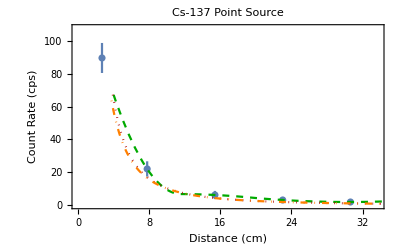

```mathematica
partacslpd=Multicolumn[Join[PartACsDetectorHeight,PartACsBGDTCorrectedCountRate],2]//First;
PACSEB=Table[ErrorBar[1/32.,PartACsBGDTCorrectedRateError[[i]]],{i,Length[PartACsBGDTCorrectedRateError]}];
PartACsDataPlot=ErrorListPlot[Table[{{partacslpd[[i,1]],partacslpd[[i,2]]},PACSEB[[i]]},{i,Length[partacslpd]}],
Frame->True,
FrameTicksStyle->Directive[Black,18],
FrameLabel->{Style["Distance (cm)",20],Style["Count Rate (cps)",20]},
PlotLabel->Style["Cs-137 Point Source",24],
ImageSize->Full,
PlotRange->{{0,1.1*(Max[PartACsDetectorHeight]+1/32.)},{0,1.1*Max[PartACsBGDTCorrectedCountRate]+Max[PartACsBGDTCorrectedRateError]}},
PlotLegends->Placed[{"Measured"},{0.85,0.85}]];
partacsinterp=Interpolation[partacslpd,InterpolationOrder->2,Method->"Spline"];
pacsinterpplot=Plot[partacsinterp[x],{x,0,35},PlotStyle->{Darker[Green],Dashed},PlotLegends->Placed[{"Interpolation of Data"},{0.85,0.85}]];
pacse5=Plot[Eq5[pacsa,0.005,1,Pi*((2.54*(1+5/16))*0.5)^2,r,0.0000949],{r,0,35},PlotStyle->{Darker[Red],Dotted},PlotLegends->Placed[{"Theoretical Point Source"},{0.85,0.85}]];
pacse6=Plot[Eq6[pacsa,0.005,d,((2.54*(1+5/16))*0.5),0.0000949],{d,0,35},PlotStyle->{Orange,DotDashed},PlotLegends->Placed[{"Close-in Point Source"},{0.85,0.85}]];
Show[PartACsDataPlot,pacsinterpplot,pacse5,pacse6]
```

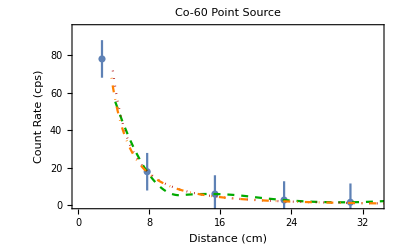

```mathematica
partacolpd=Multicolumn[Join[PartACoDetectorHeight,PartACoBGDTCorrectedCountRate],2]//First;
partacolpderr=Table[ErrorBar[2.54/32.,10],{i,Length[partacolpd]}];
PartACoDataPlot=ErrorListPlot[Table[{partacolpd[[i]],partacolpderr[[i]]},{i,1,Length[partacolpd]}],
Frame->True,
FrameTicksStyle->Directive[Black,18],
FrameLabel->{Style["Distance (cm)",20],Style["Count Rate (cps)",20]},
PlotLabel->Style["Co-60 Point Source",24],
ImageSize->Full,
PlotRange->{{0,1.1*(Max[PartACoDetectorHeight]+1/32.)},{0,1.1*Max[PartACoBGDTCorrectedCountRate]+Max[PartACoBGTDCorrectedRateError]}},
PlotLegends->Placed[{"Measured"},{0.85,0.85}]];
partacointerp=Interpolation[partacolpd,InterpolationOrder->2,Method->"Spline"];
PartAInterpPlot=Plot[partacointerp[x],{x,0,35},PlotStyle->{Darker[Green],Dashed},PlotLegends->Placed[{"Interpolation of Data"},{0.85,0.85}]];
pacoe5=Plot[Eq5[pacoa,0.02,1,Pi*((2.54*(1+5/16))*0.5)^2,r,0.0000949],{r,0,35},PlotStyle->{Darker[Red],Dotted},PlotLegends->Placed[{"Theoretical Point Source"},{0.85,0.85}]];
pacoe6=Plot[Eq6[pacoa,0.02,d,((2.54*(1+5/16))*0.5),0.0000949],{d,0,35},PlotStyle->{Orange,DotDashed},PlotLegends->Placed[{"Close-in Point Source"},{0.85,0.85}]];
Show[PartACoDataPlot,PartAInterpPlot,pacoe5,pacoe6]
```

6. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 over equation 8.7 in the text with an error of no more than 5% for each source. Compare the two answers and discuss if they are different or not and whether they agree with our rule of thumb.

Note: use the best guess geometric efficiency equation based upon the inspection of the plot from question 6.

For Cs-137:

Line Source

1. Make a table for the line source data with the same information contained within the table for the point source analysis.

```mathematica
PartBDistance={2, 6, 10, 14, 18, 22, 26, 30, 34}*2.54 (* cm *);
PartBCounts = {48692, 16490, 7018, 3564, 1988, 1222, 795, 514, 332};
PartBTime=60 (* seconds *);
PartBCountRate=PartBCounts/PartBTime//N
PartBBGCorrCountRate=PartBCountRate-BackgroundCountRate
PartBBGCorrCountErrors=√(PartBCounts/PartBTime^2+BackgroundCountRateError^2);
PartBBGDTCorrCountRate=DTC[PartBBGCorrCountRate]
PartBBGDTCorrErrors=DTCError[PartBBGCorrCountRate,PartBBGCorrCountErrors]
```

{811.533,274.833,116.967,59.4,33.1333,20.3667,13.25,8.56667,5.53333}

{810.963,274.263,116.397,58.83,32.5633,19.7967,12.68,7.99667,4.96333}

{668.851,255.877,112.952,57.937,32.2879,19.6945,12.638,7.97995,4.95689}

{2.50187,1.86327,1.31545,0.965935,0.731853,0.578233,0.468826,0.378776,0.305997}

```mathematica
PartBPlotData=Table[{{PartBDistance[[i]],PartBBGDTCorrCountRate[[i]]},ErrorBar[2.54*0.25,PartBBGDTCorrErrors[[i]]]},{i,Length[PartBCounts]}]
```

{{{5.08,668.851},ErrorBar[0.635,2.50187]},{{15.24,255.877},ErrorBar[0.635,1.86327]},{{25.4,112.952},ErrorBar[0.635,1.31545]},{{35.56,57.937},ErrorBar[0.635,0.965935]},{{45.72,32.2879},ErrorBar[0.635,0.731853]},{{55.88,19.6945},ErrorBar[0.635,0.578233]},{{66.04,12.638},ErrorBar[0.635,0.468826]},{{76.2,7.97995},ErrorBar[0.635,0.378776]},{{86.36,4.95689},ErrorBar[0.635,0.305997]}}

```mathematica
PartBDataPlot=ErrorListPlot[PartBPlotData,
PlotRange->{{0,1.1*Max[PartBPlotData[[;;,1,1]]]},{0,1.1*Max[PartBPlotData[[;;,1,2]]]}},
Frame->True,
FrameLabel->{Style["Distance from source (cm)",20],Style["Count Rate (cps)",20]},
FrameTicksStyle->18,
PlotLabel->Style["Count Rate vs. Range for Line Source",24],
ImageSize->Full,
PlotLegends->Placed[{"Measured"},{0.85,0.85}]];
```

```mathematica
Range[Length[PartBCountRate]]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
TableForm[Map[{PartBDistance[[#]],PartBCountRate[[#]],PartBBGCorrCountRate[[#]],PartBBGDTCorrCountRate[[#]],PartBBGDTCorrErrors[[#]]}&,Range[Length[PartBDistance]]],TableHeadings->{None,{"Distance (cm)", "Count rate (cps)", "BG Corrected", "BG/Deadtime Corrected", "Error"}}]
```

Distance (cm) | Count rate (cps) | BG Corrected | BG/Deadtime Corrected | Error
5.08 | 811.533 | 810.963 | 668.851 | 2.50187
15.24 | 274.833 | 274.263 | 255.877 | 1.86327
25.4 | 116.967 | 116.397 | 112.952 | 1.31545
35.56 | 59.4 | 58.83 | 57.937 | 0.965935
45.72 | 33.1333 | 32.5633 | 32.2879 | 0.731853
55.88 | 20.3667 | 19.7967 | 19.6945 | 0.578233
66.04 | 13.25 | 12.68 | 12.638 | 0.468826
76.2 | 8.56667 | 7.99667 | 7.97995 | 0.378776
86.36 | 5.53333 | 4.96333 | 4.95689 | 0.305997

2. Determine the total line energetic photon emission activity (E_γ≥30keV) with uncertainty. Assume the source strength of each source is known to ±5%.

```mathematica
PartBSourceAges={24-2,60,60+6,60,24-2}; (* months *)
PartBHalfLife=30.08*12 (* months *);
PartBSingleSourceActivity=10^-5*3.7*10^10
PartBActivity=Total[PartBSingleSourceActivity*Exp[-Log[2.]/PartBHalfLife*PartBSourceAges]]
PartBActivityError=√Total[(0.05*PartBSingleSourceActivity)^2*Exp[-2*Log[2.]/PartBHalfLife*PartBSourceAges]]//N
```

370000.

1.69481×10^6

37924.7

```mathematica
PartBPhotonActivity=0.91963*PartBActivity
PartBPhotonActivityError=0.91963*PartBActivityError
```

1.5586×10^6

34876.7

The total line energetic photon emission activity is 1.56*10^6±3*10^4 photons per second.

3. Create a function that can be plotted that will provide the count rate versus distance for the line source data.

```mathematica
(*PartBPhotonFunction[d_]=PartBPhotonActivity*0.05*(π*Radius^2)/(4*π*d^2)*Exp[-muCsAir*d];*)
PartBA1=0.04*PartBPhotonActivity;
PartBA2=0.04*PartBPhotonActivity;
PartBSourceLength=8*2.54;
PartBPhotonFunction[d_]=Piecewise[{{PartBA1*1/d^2,d>PartBSourceLength/2},{PartBA2*1/d,d<PartBSourceLength/2}}]
```

Piecewise[{{62344./d^2, d>10.16}, {62344./d, d<10.16}, {0, True}}]

4. Plot the properly corrected count rate (with error bars) vs. distance. Interpolate between the data points with an interpolation order of 2. Also include the theoretical detection efficiency for both a line source and a 1/r^2 (point) source. Include a legend to identify which curve is which (i.e., data vs. calculated).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

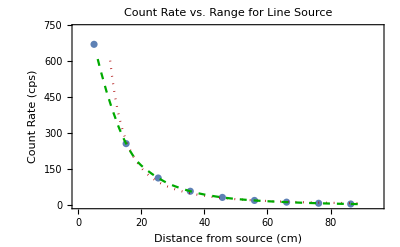

```mathematica
PartBCurvePlot=Plot[PartBPhotonFunction[d],{d,0,35*2.54},PlotStyle->{Darker[Red],Dotted},PlotLegends->Placed[{"Theoretical piecewise"},{0.85,0.85}]];
PartBInterpData=Multicolumn[Join[PartBDistance,PartBBGDTCorrCountRate],2]//First;
PartBInterp=Interpolation[PartBInterpData,InterpolationOrder->2,Method->"Spline"];
PartBInterpPlot=Plot[PartBInterp[d],{d,0,35*2.54},PlotStyle->{Darker[Green],Dashed},PlotLegends->Placed[{"Interpolation"},{0.85,0.85}]];
Show[PartBDataPlot,PartBCurvePlot,PartBInterpPlot]
```

5. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 in the text vs. the appropriate line source equation with an error of no more than 5%. Does the result agree with our rule of thumb?

The distance at which this line source can be treated as a point source (equation 8.8) is approximately equal to 10.6 cm, or L/2.

Area Source

1. Make a table for the square source data with the same information contained within the table for the point source analysis.

```mathematica
PartCDistance=List[6,9,12,15,18,21,24,27,30,33,36,39,42]*2.54 (* cm *);
PartCCounts={9385,5086,2927,1818,1167,767,550,1222,1000,775,655,506,480};
PartCTimes={60,60,60,60,60,60,60,200,200,200,200,200,200};
PartCCountRates=PartCCounts/PartCTimes//N
PartCCountRateErrors=√(PartCCounts/PartCTimes^2)//N
PartCDistanceError=0.25*2.54;
PartCBGCorrRates=PartCCountRates-BackgroundCountRate
PartCBGCorrRateErrors=√(PartCCountRateErrors^2+BackgroundCountRateError^2)
PartCBGDTCorrRates=DTC[PartCBGCorrRates]
PartCBGDTCorrRateErrrors=DTCError[PartCBGCorrRates,PartCBGCorrRateErrors]
```

{156.417,84.7667,48.7833,30.3,19.45,12.7833,9.16667,6.11,5.,3.875,3.275,2.53,2.4}

{1.6146,1.1886,0.901696,0.710634,0.569356,0.461579,0.390868,0.174786,0.158114,0.139194,0.127965,0.112472,0.109545}

{155.847,84.1967,48.2133,29.73,18.88,12.2133,8.59667,5.54,4.43,3.305,2.705,1.96,1.83}

{1.61519,1.1894,0.902749,0.711969,0.571022,0.463633,0.393291,0.180139,0.164012,0.14586,0.135185,0.120623,0.117898}

{149.733,82.3794,47.6119,29.5002,18.7871,12.1744,8.57735,5.53197,4.42486,3.30214,2.70308,1.95899,1.82912}

{1.49095,1.13861,0.880367,0.701006,0.565415,0.46068,0.391525,0.179617,0.163632,0.145607,0.134994,0.1205,0.117785}

```mathematica
TableForm[Map[{PartCDistance[[#]],PartCCountRates[[#]],PartCBGCorrRates[[#]],PartCBGDTCorrRates[[#]],PartCBGDTCorrRateErrrors[[#]]}&,Range[Length[PartCCounts]]],TableHeadings->{None,{"Distance (cm)", "Count Rate (cps)","BG Corrected", "BG/DT Corrected", "Error"}}]
```

Distance (cm) | Count Rate (cps) | BG Corrected | BG/DT Corrected | Error
15.24 | 156.417 | 155.847 | 149.733 | 1.49095
22.86 | 84.7667 | 84.1967 | 82.3794 | 1.13861
30.48 | 48.7833 | 48.2133 | 47.6119 | 0.880367
38.1 | 30.3 | 29.73 | 29.5002 | 0.701006
45.72 | 19.45 | 18.88 | 18.7871 | 0.565415
53.34 | 12.7833 | 12.2133 | 12.1744 | 0.46068
60.96 | 9.16667 | 8.59667 | 8.57735 | 0.391525
68.58 | 6.11 | 5.54 | 5.53197 | 0.179617
76.2 | 5. | 4.43 | 4.42486 | 0.163632
83.82 | 3.875 | 3.305 | 3.30214 | 0.145607
91.44 | 3.275 | 2.705 | 2.70308 | 0.134994
99.06 | 2.53 | 1.96 | 1.95899 | 0.1205
106.68 | 2.4 | 1.83 | 1.82912 | 0.117785

2. Determine the total square energetic photon emission activity (E_γ≥30keV) with uncertainty. Assume the source strength of each source is known to ±5%.

```mathematica
PartCSourceAges={22,22,22,22,60,60,60,60,60,60,60,66,66,62,61}; (* months *)
PartCInitialSourceStrength=10*10^-6*3.7*10^10 (* Bq *);
PartCHalfLife=30.08*12 (* months *);
PartCActivity=Total[PartCInitialSourceStrength*Exp[-Log[2]/PartCHalfLife*PartCSourceAges]]
PartCActivityError=√Total[(0.05*PartCInitialSourceStrength)^2*Exp[-2*Log[2.]/PartCHalfLife*PartCSourceAges]]//N
```

5.0364×10^6

65057.6

The Source activity was 5.04*10^6±7*10^4 photons per second

3. Create a function that can be plotted that will provide the total count rate versus distance for the square source data.

```mathematica
AreaOmega[d_,a_,b_]:=1/(4 π) ArcTan[(a*b)/(d*√(a^2+b^2+d^2))];
PartCDetected[d_,a_,b_]:=PartCActivity*AreaOmega[d,a,b]/4/π*Exp[-muCsAir*d];
```

4. Plot the properly corrected count rate (with error bars) vs. distance. Interpolate between the data point with an interpolation order of 2. Also include the theoretical detection efficiency for a square source and a 1/r^2 (point) source. Include a legend to identify which curve is which (i.e., data vs. calculated).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

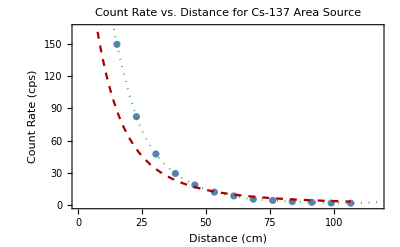

```mathematica
PartCPlotData=Table[{{PartCDistance[[i]],PartCBGDTCorrRates[[i]]},ErrorBar[PartCDistanceError,PartCBGDTCorrRateErrrors[[i]]]},{i,Length[PartCDistance]}];
PartCDataPlot=ErrorListPlot[PartCPlotData,
Frame->True,
FrameLabel->{Style["Distance (cm)",20],Style["Count Rate (cps)",20]},
PlotLabel->Style["Count Rate vs. Distance for Cs-137 Area Source",24],
FrameTicksStyle->18,
PlotLegends->Placed[{"Measured"},{0.85,0.85}],
PlotRange->{{0,1.1*(42*2.54)},{0,1.1*Max[PartCPlotData[[;;,1,2]]]}},
ImageSize->Full];
PartCInterpFunc=Interpolation[PartCPlotData[[;;,1]],InterpolationOrder->2,Method->"Spline"];
PartCInterpPlot=Plot[PartCInterpFunc[d],{d,0,120},PlotStyle->{Darker[Green],Dotted},PlotLegends->Placed[{"Interpolation"},{0.85,0.85}]];
PartCTheoryPlot=Plot[150/25000*PartCDetected[d,4*2.54,8*2.54],{d,0,42*2.54},PlotStyle->{Darker[Red],Dashed},PlotLegends->Placed[{"Theoretical"},{0.85,0.85}]];
Show[PartCDataPlot,PartCInterpPlot,PartCTheoryPlot]
```

5. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 over equation 8.11 in the text with an error of no more than 5%. Does the result agree with our rule of thumb?